```mathematica
testSize=All;
testRNG[r_]:=(
n=Length[r];
drs=Sort[r];
Do[drs[[i]]=drs[[i]]-drs[[i-1]],{i,n,2,-1}];
λ=1/Mean[drs];
walks=Table[Accumulate[2r[[100(i-1)+1;;100i]]-1],{i,1,Floor[n/100]}];
Grid[{
{
ListPlot[r[[1;;If[n>10000,10000,All]]],Joined->False,PlotRange->{All,{0,1}},AspectRatio->1],
Show[Histogram[r,100,"PDF",AspectRatio->1],Plot[PDF[UniformDistribution[],x],{x,0,1}]],
Show[Histogram[r,100,"CDF",AspectRatio->1],Plot[CDF[UniformDistribution[],x],{x,0,1}]],
Show[Histogram[drs,100,"PDF",AspectRatio->1],Plot[PDF[ExponentialDistribution[λ],x],{x,0,Max[drs]},PlotRange->All]]
},{
ListPlot[Partition[r,2][[1;;If[n>20000,10000,All]]],Joined->False,PlotRange->{{0,1},{0,1}},AspectRatio->1],
ListLinePlot[walks,PlotRange->{All,{Min[walks],Max[walks]}},AspectRatio->1,PlotStyle->Thin],
TableForm[{{"","Unif Dist?","Exp Spaces?"},
{"CVM",CramerVonMisesTest[r,UniformDistribution[],{"PValue","ShortTestConclusion"}],CramerVonMisesTest[drs,ExponentialDistribution[λ],{"PValue","ShortTestConclusion"}]},
{"AD",AndersonDarlingTest[r,UniformDistribution[],{"PValue","ShortTestConclusion"}],AndersonDarlingTest[drs,ExponentialDistribution[λ],{"PValue","ShortTestConclusion"}]},
{"PC2",PearsonChiSquareTest[r,UniformDistribution[],{"PValue","ShortTestConclusion"}],PearsonChiSquareTest[drs,ExponentialDistribution[λ],{"PValue","ShortTestConclusion"}]}}],
SpanFromLeft
}
}]
)
```

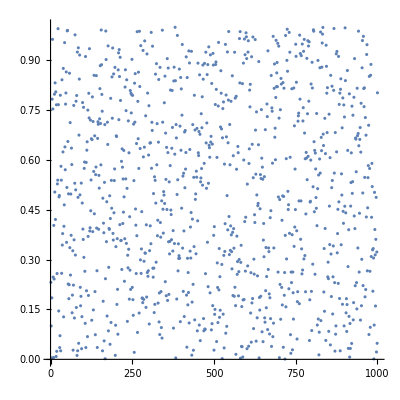
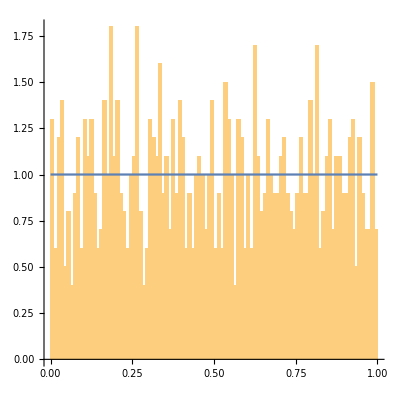
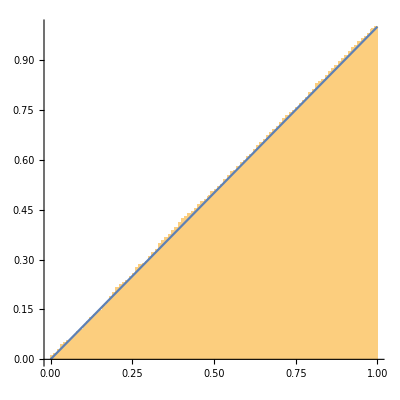
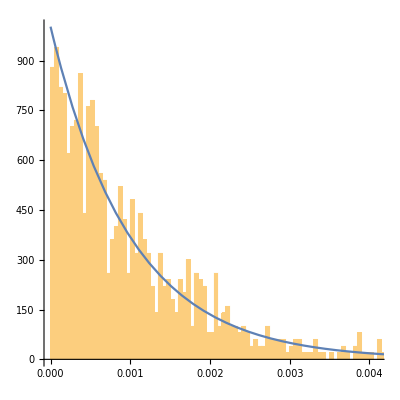
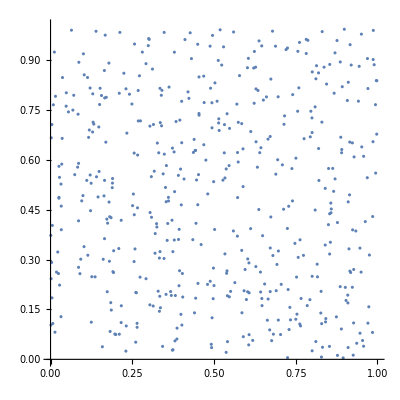
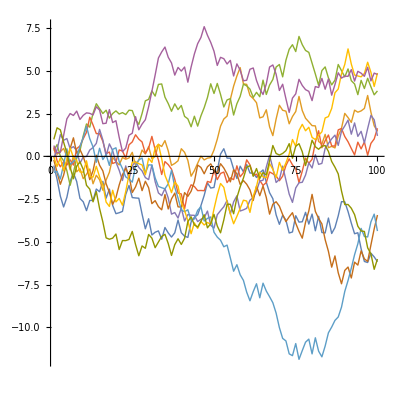
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  | Unif Dist? | Exp Spaces?
CVM | 0.993707810736764
Do not reject | 0.478357
Do not reject
AD | 0.9895211872119
Do not reject | 0.53633
Do not reject
PC2 | 0.73726243132225
Do not reject | 0.3596865
Do not reject |

```mathematica
Clear[xi];
xi=RandomReal[1,1000,WorkingPrecision->16];
testRNG[xi]
```

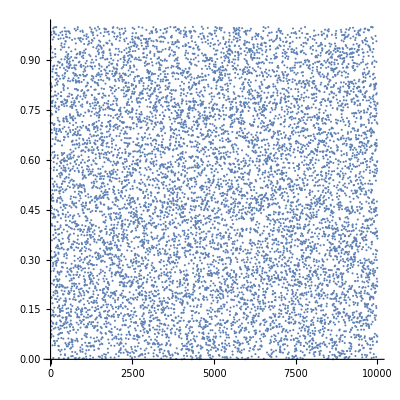
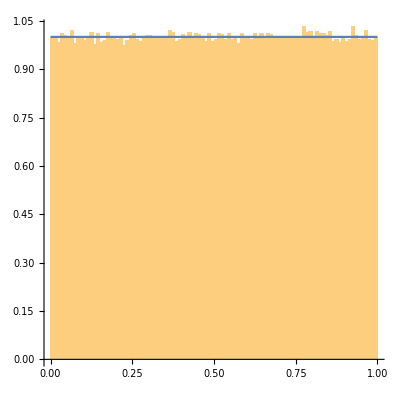
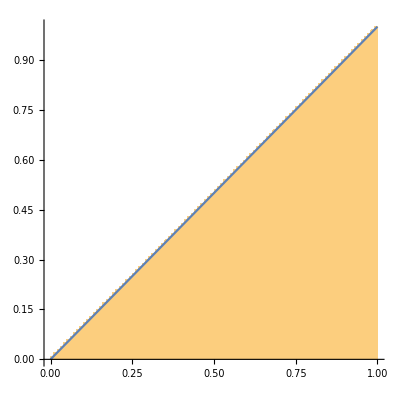
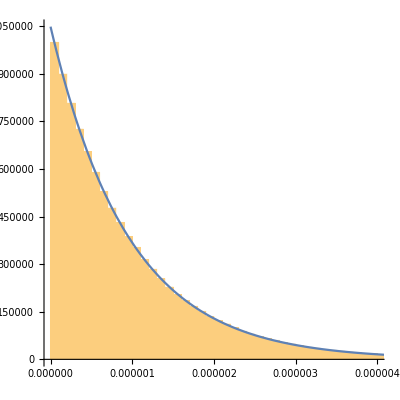
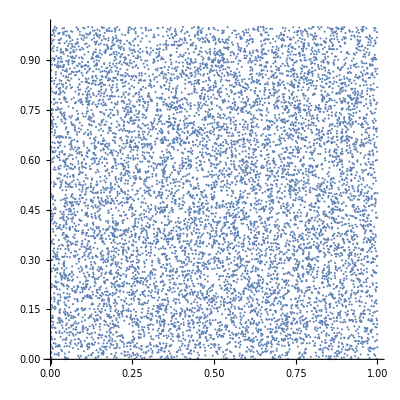
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  | Unif Dist? | Exp Spaces?
CVM | 0.094415313210815
Do not reject | 0.242064
Do not reject
AD | 0.13683785399
Do not reject | 0
Reject
PC2 | 0.3080856260237611
Do not reject | 4.619157×10^-79
Reject |

```mathematica
Clear[xi];SetDirectory[NotebookDirectory[]];
xi=ReadList["randoms19937.tst",Real];xi=xi[[1;;testSize]];
testRNG[xi]
```

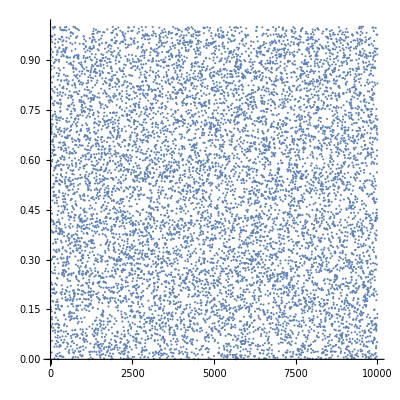
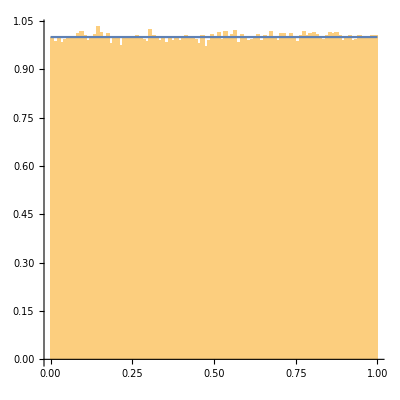
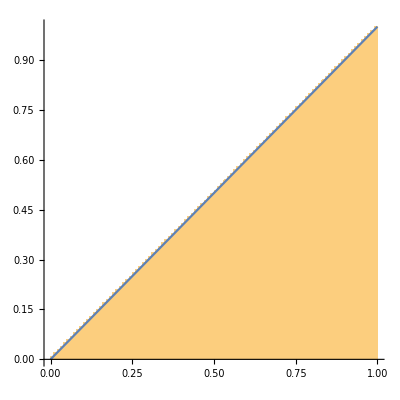
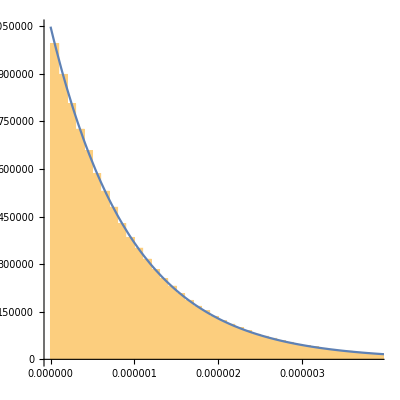
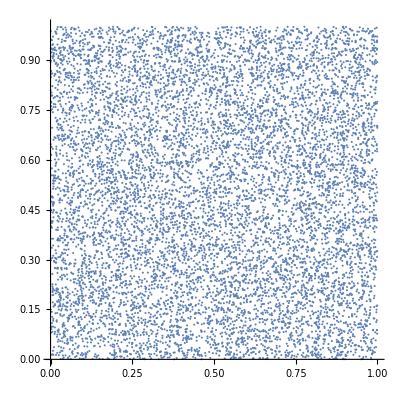
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  | Unif Dist? | Exp Spaces?
CVM | 0.11510837399362
Do not reject | 0.89
Do not reject
AD | 0.142192311189
Do not reject | 0.95
Do not reject
PC2 | 0.2550294326298676
Do not reject | 0.13886
Do not reject |

```mathematica
Clear[xi];SetDirectory[NotebookDirectory[]];
xi=ReadList["randoms19937x64.tst",Real];xi=xi[[1;;testSize]];
testRNG[xi]
```